# Homework 1

Presenter :  205978000
Name :  Shahaf Zohar

### my favorite (social) network

#### i chose the social network of friendship in a swimming team, (graph name Friendship)

```mathematica
Needs["GraphUtilities`"];
```

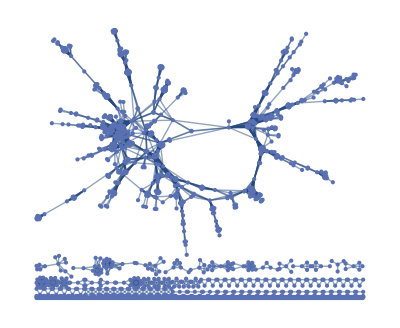

```mathematica
DiseaseNetwork= ExampleData[{"NetworkGraph", "DiseaseGeneNetwork"}]
```

```mathematica
VertexCount[DiseaseNetwork]
```

1777

```mathematica
VertexDegree[DiseaseNetwork]
```

```mathematica
node = Part[VertexList[DiseaseNetwork], Ordering[DegreeCentrality[DiseaseNetwork], All, Greater]][[1]]
```

1214

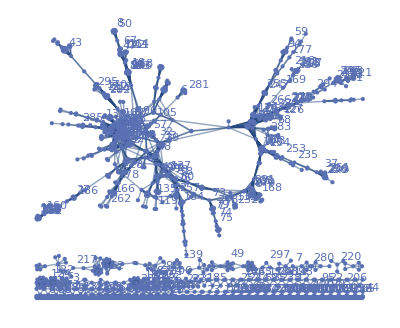

```mathematica
NewGraph= VertexReplace[DiseaseNetwork,{node -> "Adam"}];
Graph[NewGraph, VertexLabels->"Name"]
```

#### So now i pick the largest degree node in the network call Italy

#### Statistics for Adam’s Neighborhood Graph:

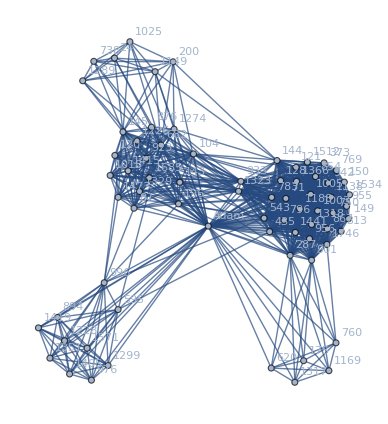

```mathematica
G=NeighborhoodGraph[NewGraph, "Adam"];
Graph[G, VertexLabels->"Name"]
```

```mathematica
EdgeCount[%6]
```

869

### Number of nodes:

```mathematica
vertexC= VertexCount[G];
Print["The graph has ", vertexC, " edges."]
```

The graph has 71 edges.

### Number of edges:

```mathematica
Edges=EdgeCount[G];
Print["The graph has ", Edges, " edges."]
```

The graph has 869 edges.

### Number Connected Components (Without Adam):

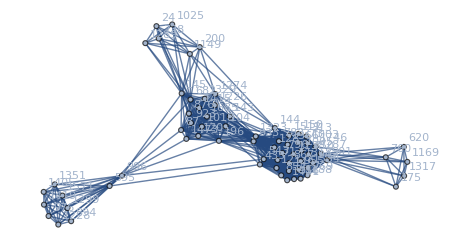

```mathematica
GwithoutAdam= VertexDelete[G,"Adam"];
Graph[GwithoutAdam, VertexLabels->"Name"]
```

```mathematica
VertexCount[%21]
```

70

```mathematica
EdgeCount[%21]
```

799

```mathematica
components= ConnectedComponents[GwithoutAdam];
numCoponents = Length[components];
Print["The graph has ", numCoponents, " Connented components."];
```

The graph has 1 Connented components.

### Size of Largest connected component (Without Adam):

```mathematica
connectedComponents=ConnectedComponents[GwithoutAdam];
largestComponentSize=Max[Length/@connectedComponents];
Print["The size of the largest connected component is ",largestComponentSize]
```

The size of the largest connected component is 70

### Degree Distribution :

```mathematica
DegreeGraphDistribution[VertexDegree[G]]
```

DegreeGraphDistribution[{70,8,34,19,22,18,34,34,21,36,25,33,33,7,24,10,40,33,33,35,36,12,7,27,8,33,8,33,36,34,33,33,18,10,38,18,49,33,33,33,10,15,33,33,18,8,33,10,7,33,18,10,21,8,10,7,33,49,18,10,34,10,18,10,33,19,34,33,10,18,34}]

{70,8,34,19,22,18,34,34,21,36,25,33,33,7,24,10,40,33,33,35,36,12,7,27,8,33,8,33,36,34,33,33,18,10,38,18,49,33,33,33,10,15,33,33,18,8,33,10,7,33,18,10,21,8,10,7,33,49,18,10,34,10,18,10,33,19,34,33,10,18,34}

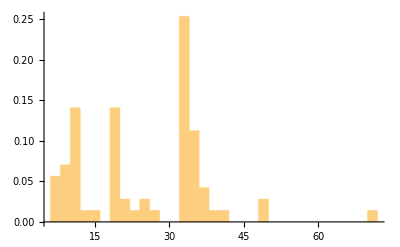

```mathematica
Deg = VertexDegree[G]
Histogram[Deg, 20 ,"Probability"]
```

### Consider Adam’s Ego network: How many triangles Adam have in his Ego networks (Including Adam) . How many triangles in the Neighborhood graph :

```mathematica
cycles= FindCycle[{G ,"Adam"},{3},All]
Length[cycles]
```

{{Adam<->783,783<->796,796<->Adam},{Adam<->796,796<->769,769<->Adam},{Adam<->769,769<->854,854<->Adam},{Adam<->783,783<->854,854<->Adam},{Adam<->796,796<->854,854<->Adam},{Adam<->854,854<->750,750<->Adam},{Adam<->796,796<->750,750<->Adam},{Adam<->783,783<->750,750<->Adam},{Adam<->769,769<->750,750<->Adam},{Adam<->750,750<->867,867<->Adam},{Adam<->769,769<->867,867<->Adam},{Adam<->783,783<->867,867<->Adam},{Adam<->796,796<->867,867<->Adam},{Adam<->854,854<->867,867<->Adam},{Adam<->750,750<->942,942<->Adam},{Adam<->769,769<->942,942<->Adam},{Adam<->783,783<->942,942<->Adam},{Adam<->796,796<->942,942<->Adam},{Adam<->854,854<->942,942<->Adam},{Adam<->867,867<->942,942<->Adam},{Adam<->750,750<->955,955<->Adam},{Adam<->769,769<->955,955<->Adam},{Adam<->783,783<->955,955<->Adam},{Adam<->796,796<->955,955<->Adam},{Adam<->854,854<->955,955<->Adam},{Adam<->867,867<->955,955<->Adam},{Adam<->942,942<->955,955<->Adam},{Adam<->750,750<->956,956<->Adam},{Adam<->783,783<->956,956<->Adam},{Adam<->796,796<->956,956<->Adam},{Adam<->854,854<->956,956<->Adam},{Adam<->867,867<->956,956<->Adam},{Adam<->942,942<->956,956<->Adam},{Adam<->955,955<->956,956<->Adam},{Adam<->1419,1419<->1571,1571<->Adam},{Adam<->750,750<->1003,1003<->Adam},{Adam<->769,769<->1003,1003<->Adam},{Adam<->783,783<->1003,1003<->Adam},{Adam<->796,796<->1003,1003<->Adam},{Adam<->854,854<->1003,1003<->Adam},{Adam<->867,867<->1003,1003<->Adam},{Adam<->942,942<->1003,1003<->Adam},{Adam<->955,955<->1003,1003<->Adam},{Adam<->956,956<->1003,1003<->Adam},{Adam<->1419,1419<->1405,1405<->Adam},{Adam<->1571,1571<->1405,1405<->Adam},{Adam<->750,750<->1005,1005<->Adam},{Adam<->769,769<->1005,1005<->Adam},{Adam<->783,783<->1005,1005<->Adam},{Adam<->796,796<->1005,1005<->Adam},{Adam<->854,854<->1005,1005<->Adam},{Adam<->867,867<->1005,1005<->Adam},{Adam<->942,942<->1005,1005<->Adam},{Adam<->955,955<->1005,1005<->Adam},{Adam<->956,956<->1005,1005<->Adam},{Adam<->1003,1003<->1005,1005<->Adam},{Adam<->1419,1419<->1351,1351<->Adam},{Adam<->1571,1571<->1351,1351<->Adam},{Adam<->1405,1405<->1351,1351<->Adam},{Adam<->750,750<->1138,1138<->Adam},{Adam<->769,769<->1138,1138<->Adam},{Adam<->783,783<->1138,1138<->Adam},{Adam<->796,796<->1138,1138<->Adam},{Adam<->854,854<->1138,1138<->Adam},{Adam<->867,867<->1138,1138<->Adam},{Adam<->942,942<->1138,1138<->Adam},{Adam<->955,955<->1138,1138<->Adam},{Adam<->956,956<->1138,1138<->Adam},{Adam<->1003,1003<->1138,1138<->Adam},{Adam<->1005,1005<->1138,1138<->Adam},{Adam<->1419,1419<->1299,1299<->Adam},{Adam<->1571,1571<->1299,1299<->Adam},{Adam<->1405,1405<->1299,1299<->Adam},{Adam<->1351,1351<->1299,1299<->Adam},{Adam<->750,750<->1188,1188<->Adam},{Adam<->769,769<->1188,1188<->Adam},{Adam<->783,783<->1188,1188<->Adam},{Adam<->796,796<->1188,1188<->Adam},{Adam<->854,854<->1188,1188<->Adam},{Adam<->867,867<->1188,1188<->Adam},{Adam<->942,942<->1188,1188<->Adam},{Adam<->955,955<->1188,1188<->Adam},{Adam<->956,956<->1188,1188<->Adam},{Adam<->1003,1003<->1188,1188<->Adam},{Adam<->1005,1005<->1188,1188<->Adam},{Adam<->1138,1138<->1188,1188<->Adam},{Adam<->1419,1419<->1228,1228<->Adam},{Adam<->1571,1571<->1228,1228<->Adam},{Adam<->1405,1405<->1228,1228<->Adam},{Adam<->1351,1351<->1228,1228<->Adam},{Adam<->1299,1299<->1228,1228<->Adam},{Adam<->750,750<->1318,1318<->Adam},{Adam<->769,769<->1318,1318<->Adam},{Adam<->783,783<->1318,1318<->Adam},{Adam<->796,796<->1318,1318<->Adam},{Adam<->854,854<->1318,1318<->Adam},{Adam<->867,867<->1318,1318<->Adam},{Adam<->942,942<->1318,1318<->Adam},{Adam<->955,955<->1318,1318<->Adam},{Adam<->956,956<->1318,1318<->Adam},{Adam<->1003,1003<->1318,1318<->Adam},{Adam<->1005,1005<->1318,1318<->Adam},{Adam<->1138,1138<->1318,1318<->Adam},{Adam<->1188,1188<->1318,1318<->Adam},{Adam<->1419,1419<->976,976<->Adam},{Adam<->1571,1571<->976,976<->Adam},{Adam<->1405,1405<->976,976<->Adam},{Adam<->1351,1351<->976,976<->Adam},{Adam<->1299,1299<->976,976<->Adam},{Adam<->1228,1228<->976,976<->Adam},{Adam<->750,750<->1366,1366<->Adam},{Adam<->769,769<->1366,1366<->Adam},{Adam<->796,796<->1366,1366<->Adam},{Adam<->854,854<->1366,1366<->Adam},{Adam<->867,867<->1366,1366<->Adam},{Adam<->942,942<->1366,1366<->Adam},{Adam<->955,955<->1366,1366<->Adam},{Adam<->956,956<->1366,1366<->Adam},{Adam<->1003,1003<->1366,1366<->Adam},{Adam<->1005,1005<->1366,1366<->Adam},{Adam<->1138,1138<->1366,1366<->Adam},{Adam<->1188,1188<->1366,1366<->Adam},{Adam<->1318,1318<->1366,1366<->Adam},{Adam<->1419,1419<->894,894<->Adam},{Adam<->1571,1571<->894,894<->Adam},{Adam<->1405,1405<->894,894<->Adam},{Adam<->1351,1351<->894,894<->Adam},{Adam<->1299,1299<->894,894<->Adam},{Adam<->1228,1228<->894,894<->Adam},{Adam<->976,976<->894,894<->Adam},{Adam<->750,750<->1441,1441<->Adam},{Adam<->769,769<->1441,1441<->Adam},{Adam<->783,783<->1441,1441<->Adam},{Adam<->796,796<->1441,1441<->Adam},{Adam<->854,854<->1441,1441<->Adam},{Adam<->867,867<->1441,1441<->Adam},{Adam<->942,942<->1441,1441<->Adam},{Adam<->955,955<->1441,1441<->Adam},{Adam<->956,956<->1441,1441<->Adam},{Adam<->1003,1003<->1441,1441<->Adam},{Adam<->1005,1005<->1441,1441<->Adam},{Adam<->1138,1138<->1441,1441<->Adam},{Adam<->1188,1188<->1441,1441<->Adam},{Adam<->1318,1318<->1441,1441<->Adam},{Adam<->1366,1366<->1441,1441<->Adam},{Adam<->1419,1419<->595,595<->Adam},{Adam<->1571,1571<->595,595<->Adam},{Adam<->1405,1405<->595,595<->Adam},{Adam<->1351,1351<->595,595<->Adam},{Adam<->1299,1299<->595,595<->Adam},{Adam<->1228,1228<->595,595<->Adam},{Adam<->976,976<->595,595<->Adam},{Adam<->894,894<->595,595<->Adam},{Adam<->750,750<->1512,1512<->Adam},{Adam<->769,769<->1512,1512<->Adam},{Adam<->796,796<->1512,1512<->Adam},{Adam<->854,854<->1512,1512<->Adam},{Adam<->867,867<->1512,1512<->Adam},{Adam<->942,942<->1512,1512<->Adam},{Adam<->955,955<->1512,1512<->Adam},{Adam<->956,956<->1512,1512<->Adam},{Adam<->1003,1003<->1512,1512<->Adam},{Adam<->1005,1005<->1512,1512<->Adam},{Adam<->1138,1138<->1512,1512<->Adam},{Adam<->1188,1188<->1512,1512<->Adam},{Adam<->1318,1318<->1512,1512<->Adam},{Adam<->1441,1441<->1512,1512<->Adam},{Adam<->1512,1512<->435,435<->Adam},{Adam<->1441,1441<->435,435<->Adam},{Adam<->1366,1366<->435,435<->Adam},{Adam<->1318,1318<->435,435<->Adam},{Adam<->1188,1188<->435,435<->Adam},{Adam<->1138,1138<->435,435<->Adam},{Adam<->1005,1005<->435,435<->Adam},{Adam<->1003,1003<->435,435<->Adam},{Adam<->956,956<->435,435<->Adam},{Adam<->955,955<->435,435<->Adam},{Adam<->942,942<->435,435<->Adam},{Adam<->867,867<->435,435<->Adam},{Adam<->854,854<->435,435<->Adam},{Adam<->796,796<->435,435<->Adam},{Adam<->783,783<->435,435<->Adam},{Adam<->769,769<->435,435<->Adam},{Adam<->750,750<->435,435<->Adam},{Adam<->595,595<->435,435<->Adam},{Adam<->435,435<->1534,1534<->Adam},{Adam<->750,750<->1534,1534<->Adam},{Adam<->769,769<->1534,1534<->Adam},{Adam<->783,783<->1534,1534<->Adam},{Adam<->796,796<->1534,1534<->Adam},{Adam<->854,854<->1534,1534<->Adam},{Adam<->867,867<->1534,1534<->Adam},{Adam<->942,942<->1534,1534<->Adam},{Adam<->955,955<->1534,1534<->Adam},{Adam<->956,956<->1534,1534<->Adam},{Adam<->1003,1003<->1534,1534<->Adam},{Adam<->1005,1005<->1534,1534<->Adam},{Adam<->1138,1138<->1534,1534<->Adam},{Adam<->1188,1188<->1534,1534<->Adam},{Adam<->1318,1318<->1534,1534<->Adam},{Adam<->1366,1366<->1534,1534<->Adam},{Adam<->1441,1441<->1534,1534<->Adam},{Adam<->1512,1512<->1534,1534<->Adam},{Adam<->1534,1534<->373,373<->Adam},{Adam<->1512,1512<->373,373<->Adam},{Adam<->1441,1441<->373,373<->Adam},{Adam<->1366,1366<->373,373<->Adam},{Adam<->1318,1318<->373,373<->Adam},{Adam<->1188,1188<->373,373<->Adam},{Adam<->1138,1138<->373,373<->Adam},{Adam<->1005,1005<->373,373<->Adam},{Adam<->1003,1003<->373,373<->Adam},{Adam<->956,956<->373,373<->Adam},{Adam<->955,955<->373,373<->Adam},{Adam<->942,942<->373,373<->Adam},{Adam<->867,867<->373,373<->Adam},{Adam<->854,854<->373,373<->Adam},{Adam<->796,796<->373,373<->Adam},{Adam<->783,783<->373,373<->Adam},{Adam<->769,769<->373,373<->Adam},{Adam<->750,750<->373,373<->Adam},{Adam<->435,435<->373,373<->Adam},{Adam<->894,894<->996,996<->Adam},{Adam<->976,976<->996,996<->Adam},{Adam<->1228,1228<->996,996<->Adam},{Adam<->1299,1299<->996,996<->Adam},{Adam<->1351,1351<->996,996<->Adam},{Adam<->1405,1405<->996,996<->Adam},{Adam<->1571,1571<->996,996<->Adam},{Adam<->1419,1419<->996,996<->Adam},{Adam<->595,595<->996,996<->Adam},{Adam<->1534,1534<->313,313<->Adam},{Adam<->1512,1512<->313,313<->Adam},{Adam<->1441,1441<->313,313<->Adam},{Adam<->1366,1366<->313,313<->Adam},{Adam<->1318,1318<->313,313<->Adam},{Adam<->1188,1188<->313,313<->Adam},{Adam<->1138,1138<->313,313<->Adam},{Adam<->1005,1005<->313,313<->Adam},{Adam<->1003,1003<->313,313<->Adam},{Adam<->956,956<->313,313<->Adam},{Adam<->955,955<->313,313<->Adam},{Adam<->942,942<->313,313<->Adam},{Adam<->867,867<->313,313<->Adam},{Adam<->854,854<->313,313<->Adam},{Adam<->796,796<->313,313<->Adam},{Adam<->783,783<->313,313<->Adam},{Adam<->769,769<->313,313<->Adam},{Adam<->750,750<->313,313<->Adam},{Adam<->435,435<->313,313<->Adam},{Adam<->373,373<->313,313<->Adam},{Adam<->313,313<->543,543<->Adam},{Adam<->373,373<->543,543<->Adam},{Adam<->435,435<->543,543<->Adam},{Adam<->750,750<->543,543<->Adam},{Adam<->769,769<->543,543<->Adam},{Adam<->796,796<->543,543<->Adam},{Adam<->854,854<->543,543<->Adam},{Adam<->867,867<->543,543<->Adam},{Adam<->942,942<->543,543<->Adam},{Adam<->955,955<->543,543<->Adam},{Adam<->956,956<->543,543<->Adam},{Adam<->1003,1003<->543,543<->Adam},{Adam<->1005,1005<->543,543<->Adam},{Adam<->1138,1138<->543,543<->Adam},{Adam<->1188,1188<->543,543<->Adam},{Adam<->1318,1318<->543,543<->Adam},{Adam<->1366,1366<->543,543<->Adam},{Adam<->1441,1441<->543,543<->Adam},{Adam<->1512,1512<->543,543<->Adam},{Adam<->1534,1534<->543,543<->Adam},{Adam<->996,996<->543,543<->Adam},{Adam<->543,543<->1746,1746<->Adam},{Adam<->1534,1534<->1746,1746<->Adam},{Adam<->1512,1512<->1746,1746<->Adam},{Adam<->1441,1441<->1746,1746<->Adam},{Adam<->1366,1366<->1746,1746<->Adam},{Adam<->1318,1318<->1746,1746<->Adam},{Adam<->1188,1188<->1746,1746<->Adam},{Adam<->1138,1138<->1746,1746<->Adam},{Adam<->1005,1005<->1746,1746<->Adam},{Adam<->1003,1003<->1746,1746<->Adam},{Adam<->956,956<->1746,1746<->Adam},{Adam<->955,955<->1746,1746<->Adam},{Adam<->942,942<->1746,1746<->Adam},{Adam<->867,867<->1746,1746<->Adam},{Adam<->854,854<->1746,1746<->Adam},{Adam<->796,796<->1746,1746<->Adam},{Adam<->783,783<->1746,1746<->Adam},{Adam<->769,769<->1746,1746<->Adam},{Adam<->750,750<->1746,1746<->Adam},{Adam<->435,435<->1746,1746<->Adam},{Adam<->373,373<->1746,1746<->Adam},{Adam<->313,313<->1746,1746<->Adam},{Adam<->1746,1746<->144,144<->Adam},{Adam<->313,313<->144,144<->Adam},{Adam<->373,373<->144,144<->Adam},{Adam<->435,435<->144,144<->Adam},{Adam<->750,750<->144,144<->Adam},{Adam<->769,769<->144,144<->Adam},{Adam<->783,783<->144,144<->Adam},{Adam<->796,796<->144,144<->Adam},{Adam<->854,854<->144,144<->Adam},{Adam<->867,867<->144,144<->Adam},{Adam<->942,942<->144,144<->Adam},{Adam<->955,955<->144,144<->Adam},{Adam<->956,956<->144,144<->Adam},{Adam<->1003,1003<->144,144<->Adam},{Adam<->1005,1005<->144,144<->Adam},{Adam<->1138,1138<->144,144<->Adam},{Adam<->1188,1188<->144,144<->Adam},{Adam<->1318,1318<->144,144<->Adam},{Adam<->1366,1366<->144,144<->Adam},{Adam<->1441,1441<->144,144<->Adam},{Adam<->1512,1512<->144,144<->Adam},{Adam<->1534,1534<->144,144<->Adam},{Adam<->543,543<->144,144<->Adam},{Adam<->1746,1746<->760,760<->Adam},{Adam<->144,144<->200,200<->Adam},{Adam<->760,760<->620,620<->Adam},{Adam<->200,200<->738,738<->Adam},{Adam<->760,760<->175,175<->Adam},{Adam<->620,620<->175,175<->Adam},{Adam<->200,200<->1025,1025<->Adam},{Adam<->738,738<->1025,1025<->Adam},{Adam<->200,200<->1289,1289<->Adam},{Adam<->738,738<->1289,1289<->Adam},{Adam<->1025,1025<->1289,1289<->Adam},{Adam<->144,144<->150,150<->Adam},{Adam<->543,543<->150,150<->Adam},{Adam<->1534,1534<->150,150<->Adam},{Adam<->1512,1512<->150,150<->Adam},{Adam<->1441,1441<->150,150<->Adam},{Adam<->1366,1366<->150,150<->Adam},{Adam<->1318,1318<->150,150<->Adam},{Adam<->1188,1188<->150,150<->Adam},{Adam<->1138,1138<->150,150<->Adam},{Adam<->1005,1005<->150,150<->Adam},{Adam<->1003,1003<->150,150<->Adam},{Adam<->956,956<->150,150<->Adam},{Adam<->955,955<->150,150<->Adam},{Adam<->942,942<->150,150<->Adam},{Adam<->867,867<->150,150<->Adam},{Adam<->854,854<->150,150<->Adam},{Adam<->796,796<->150,150<->Adam},{Adam<->783,783<->150,150<->Adam},{Adam<->769,769<->150,150<->Adam},{Adam<->750,750<->150,150<->Adam},{Adam<->435,435<->150,150<->Adam},{Adam<->373,373<->150,150<->Adam},{Adam<->313,313<->150,150<->Adam},{Adam<->1746,1746<->150,150<->Adam},{Adam<->144,144<->1149,1149<->Adam},{Adam<->738,738<->1149,1149<->Adam},{Adam<->1025,1025<->1149,1149<->Adam},{Adam<->1289,1289<->1149,1149<->Adam},{Adam<->144,144<->149,149<->Adam},{Adam<->543,543<->149,149<->Adam},{Adam<->1534,1534<->149,149<->Adam},{Adam<->1512,1512<->149,149<->Adam},{Adam<->1441,1441<->149,149<->Adam},{Adam<->1366,1366<->149,149<->Adam},{Adam<->1318,1318<->149,149<->Adam},{Adam<->1188,1188<->149,149<->Adam},{Adam<->1138,1138<->149,149<->Adam},{Adam<->1005,1005<->149,149<->Adam},{Adam<->1003,1003<->149,149<->Adam},{Adam<->956,956<->149,149<->Adam},{Adam<->955,955<->149,149<->Adam},{Adam<->942,942<->149,149<->Adam},{Adam<->867,867<->149,149<->Adam},{Adam<->854,854<->149,149<->Adam},{Adam<->796,796<->149,149<->Adam},{Adam<->783,783<->149,149<->Adam},{Adam<->769,769<->149,149<->Adam},{Adam<->750,750<->149,149<->Adam},{Adam<->435,435<->149,149<->Adam},{Adam<->373,373<->149,149<->Adam},{Adam<->313,313<->149,149<->Adam},{Adam<->1746,1746<->149,149<->Adam},{Adam<->150,150<->149,149<->Adam},{Adam<->144,144<->1274,1274<->Adam},{Adam<->200,200<->1274,1274<->Adam},{Adam<->1149,1149<->1274,1274<->Adam},{Adam<->144,144<->128,128<->Adam},{Adam<->543,543<->128,128<->Adam},{Adam<->1534,1534<->128,128<->Adam},{Adam<->1512,1512<->128,128<->Adam},{Adam<->1441,1441<->128,128<->Adam},{Adam<->1366,1366<->128,128<->Adam},{Adam<->1318,1318<->128,128<->Adam},{Adam<->1188,1188<->128,128<->Adam},{Adam<->1138,1138<->128,128<->Adam},{Adam<->1005,1005<->128,128<->Adam},{Adam<->1003,1003<->128,128<->Adam},{Adam<->956,956<->128,128<->Adam},{Adam<->955,955<->128,128<->Adam},{Adam<->942,942<->128,128<->Adam},{Adam<->867,867<->128,128<->Adam},{Adam<->854,854<->128,128<->Adam},{Adam<->796,796<->128,128<->Adam},{Adam<->783,783<->128,128<->Adam},{Adam<->769,769<->128,128<->Adam},{Adam<->750,750<->128,128<->Adam},{Adam<->435,435<->128,128<->Adam},{Adam<->373,373<->128,128<->Adam},{Adam<->313,313<->128,128<->Adam},{Adam<->1746,1746<->128,128<->Adam},{Adam<->150,150<->128,128<->Adam},{Adam<->149,149<->128,128<->Adam},{Adam<->1274,1274<->876,876<->Adam},{Adam<->144,144<->121,121<->Adam},{Adam<->543,543<->121,121<->Adam},{Adam<->1534,1534<->121,121<->Adam},{Adam<->1512,1512<->121,121<->Adam},{Adam<->1441,1441<->121,121<->Adam},{Adam<->1366,1366<->121,121<->Adam},{Adam<->1318,1318<->121,121<->Adam},{Adam<->1188,1188<->121,121<->Adam},{Adam<->1138,1138<->121,121<->Adam},{Adam<->1005,1005<->121,121<->Adam},{Adam<->1003,1003<->121,121<->Adam},{Adam<->956,956<->121,121<->Adam},{Adam<->955,955<->121,121<->Adam},{Adam<->942,942<->121,121<->Adam},{Adam<->867,867<->121,121<->Adam},{Adam<->854,854<->121,121<->Adam},{Adam<->796,796<->121,121<->Adam},{Adam<->783,783<->121,121<->Adam},{Adam<->769,769<->121,121<->Adam},{Adam<->750,750<->121,121<->Adam},{Adam<->435,435<->121,121<->Adam},{Adam<->373,373<->121,121<->Adam},{Adam<->313,313<->121,121<->Adam},{Adam<->1746,1746<->121,121<->Adam},{Adam<->150,150<->121,121<->Adam},{Adam<->149,149<->121,121<->Adam},{Adam<->128,128<->121,121<->Adam},{Adam<->1274,1274<->923,923<->Adam},{Adam<->876,876<->923,923<->Adam},{Adam<->144,144<->71,71<->Adam},{Adam<->543,543<->71,71<->Adam},{Adam<->1534,1534<->71,71<->Adam},{Adam<->1512,1512<->71,71<->Adam},{Adam<->1441,1441<->71,71<->Adam},{Adam<->1366,1366<->71,71<->Adam},{Adam<->1318,1318<->71,71<->Adam},{Adam<->1188,1188<->71,71<->Adam},{Adam<->1138,1138<->71,71<->Adam},{Adam<->1005,1005<->71,71<->Adam},{Adam<->1003,1003<->71,71<->Adam},{Adam<->955,955<->71,71<->Adam},{Adam<->942,942<->71,71<->Adam},{Adam<->867,867<->71,71<->Adam},{Adam<->854,854<->71,71<->Adam},{Adam<->783,783<->71,71<->Adam},{Adam<->750,750<->71,71<->Adam},{Adam<->435,435<->71,71<->Adam},{Adam<->373,373<->71,71<->Adam},{Adam<->313,313<->71,71<->Adam},{Adam<->1746,1746<->71,71<->Adam},{Adam<->150,150<->71,71<->Adam},{Adam<->149,149<->71,71<->Adam},{Adam<->128,128<->71,71<->Adam},{Adam<->121,121<->71,71<->Adam},{Adam<->1274,1274<->1018,1018<->Adam},{Adam<->876,876<->1018,1018<->Adam},{Adam<->923,923<->1018,1018<->Adam},{Adam<->1018,1018<->196,196<->Adam},{Adam<->923,923<->196,196<->Adam},{Adam<->876,876<->196,196<->Adam},{Adam<->1274,1274<->196,196<->Adam},{Adam<->996,996<->196,196<->Adam},{Adam<->796,796<->196,196<->Adam},{Adam<->783,783<->196,196<->Adam},{Adam<->71,71<->196,196<->Adam},{Adam<->196,196<->1226,1226<->Adam},{Adam<->1274,1274<->1226,1226<->Adam},{Adam<->876,876<->1226,1226<->Adam},{Adam<->923,923<->1226,1226<->Adam},{Adam<->1018,1018<->1226,1226<->Adam},{Adam<->1226,1226<->143,143<->Adam},{Adam<->1018,1018<->143,143<->Adam},{Adam<->923,923<->143,143<->Adam},{Adam<->876,876<->143,143<->Adam},{Adam<->1274,1274<->143,143<->Adam},{Adam<->543,543<->143,143<->Adam},{Adam<->783,783<->143,143<->Adam},{Adam<->143,143<->1329,1329<->Adam},{Adam<->196,196<->1329,1329<->Adam},{Adam<->1274,1274<->1329,1329<->Adam},{Adam<->876,876<->1329,1329<->Adam},{Adam<->923,923<->1329,1329<->Adam},{Adam<->1018,1018<->1329,1329<->Adam},{Adam<->1226,1226<->1329,1329<->Adam},{Adam<->1329,1329<->120,120<->Adam},{Adam<->1226,1226<->120,120<->Adam},{Adam<->1018,1018<->120,120<->Adam},{Adam<->923,923<->120,120<->Adam},{Adam<->876,876<->120,120<->Adam},{Adam<->1274,1274<->120,120<->Adam},{Adam<->196,196<->120,120<->Adam},{Adam<->143,143<->120,120<->Adam},{Adam<->120,120<->1415,1415<->Adam},{Adam<->143,143<->1415,1415<->Adam},{Adam<->196,196<->1415,1415<->Adam},{Adam<->1274,1274<->1415,1415<->Adam},{Adam<->876,876<->1415,1415<->Adam},{Adam<->923,923<->1415,1415<->Adam},{Adam<->1018,1018<->1415,1415<->Adam},{Adam<->1226,1226<->1415,1415<->Adam},{Adam<->1329,1329<->1415,1415<->Adam},{Adam<->1415,1415<->104,104<->Adam},{Adam<->1329,1329<->104,104<->Adam},{Adam<->1226,1226<->104,104<->Adam},{Adam<->1018,1018<->104,104<->Adam},{Adam<->923,923<->104,104<->Adam},{Adam<->876,876<->104,104<->Adam},{Adam<->1274,1274<->104,104<->Adam},{Adam<->1512,1512<->104,104<->Adam},{Adam<->1366,1366<->104,104<->Adam},{Adam<->783,783<->104,104<->Adam},{Adam<->121,121<->104,104<->Adam},{Adam<->196,196<->104,104<->Adam},{Adam<->143,143<->104,104<->Adam},{Adam<->120,120<->104,104<->Adam},{Adam<->104,104<->1685,1685<->Adam},{Adam<->120,120<->1685,1685<->Adam},{Adam<->143,143<->1685,1685<->Adam},{Adam<->196,196<->1685,1685<->Adam},{Adam<->1274,1274<->1685,1685<->Adam},{Adam<->876,876<->1685,1685<->Adam},{Adam<->923,923<->1685,1685<->Adam},{Adam<->1018,1018<->1685,1685<->Adam},{Adam<->1226,1226<->1685,1685<->Adam},{Adam<->1329,1329<->1685,1685<->Adam},{Adam<->1415,1415<->1685,1685<->Adam},{Adam<->1685,1685<->87,87<->Adam},{Adam<->1415,1415<->87,87<->Adam},{Adam<->1329,1329<->87,87<->Adam},{Adam<->1226,1226<->87,87<->Adam},{Adam<->1018,1018<->87,87<->Adam},{Adam<->923,923<->87,87<->Adam},{Adam<->876,876<->87,87<->Adam},{Adam<->1274,1274<->87,87<->Adam},{Adam<->996,996<->87,87<->Adam},{Adam<->196,196<->87,87<->Adam},{Adam<->143,143<->87,87<->Adam},{Adam<->120,120<->87,87<->Adam},{Adam<->104,104<->87,87<->Adam},{Adam<->1149,1149<->24,24<->Adam},{Adam<->1289,1289<->24,24<->Adam},{Adam<->1025,1025<->24,24<->Adam},{Adam<->738,738<->24,24<->Adam},{Adam<->200,200<->24,24<->Adam},{Adam<->175,175<->1317,1317<->Adam},{Adam<->620,620<->1317,1317<->Adam},{Adam<->760,760<->1317,1317<->Adam},{Adam<->175,175<->1169,1169<->Adam},{Adam<->620,620<->1169,1169<->Adam},{Adam<->760,760<->1169,1169<->Adam},{Adam<->1317,1317<->1169,1169<->Adam}}

562

### What is the maximum number of triangles a network of Adam' s network size could have (triangles that including Adam) :

For a maximum number we find all possible pairs without Adam, The maximum number of triangles is 70 choose 2 upper bound Adam’s neighborhood graph

```mathematica
Binomial[70,2]
```

```mathematica
2415
```

For us to note that the upper limit for the graph is 2415 triangles if the graph is a complete graph. Our graph has 869 edges. For a complete graph E = n(n-1)/2 the amount of arcs depends on this formula, E=71(71-1)/2 = 2485. Therefore we will note that in order to reach the maximum number of triangles we will need a complete graph, while we have 869 sides.

### Who is Adam’s best friends? Explain/show

```mathematica
Part[VertexList[GwithoutAdam], Ordering[DegreeCentrality[GwithoutAdam], All, Greater]]
Print[Part[VertexList[GwithoutAdam],Ordering[DegreeCentrality[GwithoutAdam],1,Greater][[1]]]];
```

{1323,933,287,901,783,543,144,435,1746,1512,1366,796,128,121,71,1534,1441,1318,1188,1138,1005,1003,956,955,942,867,854,769,750,373,313,150,149,682,145,196,104,1274,143,1473,87,1685,1415,1329,1226,1018,923,876,120,996,595,1571,1419,1405,1351,1299,1228,1149,976,894,200,1289,1025,760,738,24,1317,1169,620,175}

1323

### Can you divide his friends to subgroups?

```mathematica
communities=FindGraphCommunities[G]
```

{{71,121,128,144,149,150,287,313,373,435,543,750,769,783,796,854,867,901,942,955,956,1003,1005,1138,1188,1318,1366,1441,1512,1534,1746},{Adam,24,87,104,120,143,145,196,200,682,738,876,923,933,1018,1025,1149,1226,1274,1289,1323,1329,1415,1473,1685},{595,894,976,996,1228,1299,1351,1405,1419,1571},{175,620,760,1169,1317}}

```mathematica
communities=FindGraphCommunities[GwithoutAdam]
```

{{71,121,128,144,149,150,287,313,373,435,543,750,769,783,796,854,867,901,942,955,956,1003,1005,1138,1188,1318,1366,1441,1512,1534,1746},{24,87,104,120,143,145,196,200,682,738,876,923,933,1018,1025,1149,1226,1274,1289,1323,1329,1415,1473,1685},{595,894,976,996,1228,1299,1351,1405,1419,1571},{175,620,760,1169,1317}}

### Explanation

The “Louvain” method uses modularity optimization to detect communities in a graph . Modularity measures the strength of division of a network into communities, and it ranges between - 1 and 1. A higher modularity value indicates a stronger community structure in the graph . The “Louvain” algorithm aims to maximize the modularity score by iteratively optimizing communities at different levels of a hierarchy . In other words, the “Louvain” method divides the nodes of a graph into communities based on their connections and aims to maximize the modularity score of the resulting community structure .